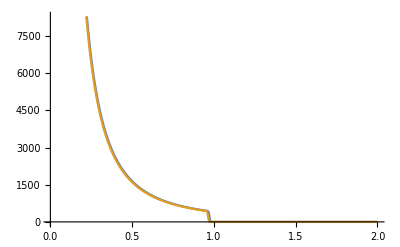

```mathematica
Rmin=10^(-3);
Rmax=2;
ρ1=1/200;
dρdr1=-3;
dlnρdr1=dρdr1/ρ1;
d2ρdr2[ρ_,r_]:=ρ[r](2ρ[r]+r*ρ'[r])-2ρ'[r]/r+(ρ'[r]^2)/ρ[r];
sol=NDSolve[{ρ''[r]==d2ρdr2[ρ,r],ρ[1]==ρ1,ρ'[1]==dρdr1},ρ,{r,Rmin,Rmax}];
ApproxDensity[r_]:=(2/ρ1)/((1+Exp[(2/ρ1)(r-1+Sqrt[ρ1]/2)])r^2);
Plot[{ρ[r]/.sol,ApproxDensity[r]},{r,Rmin,Rmax}]
```

```mathematica
DensityPlot3D[With[{r=Sqrt[x^2+y^2+z^2]},Piecewise[{{(ρ[r]/.sol)[[1]],Rmin<r<Rmax}}]],{x,y,z}∈Ball[{0,0,0},Rmax],OpacityFunction->(#&),ColorFunction->"SunsetColors"]
```

-Graphics3D-

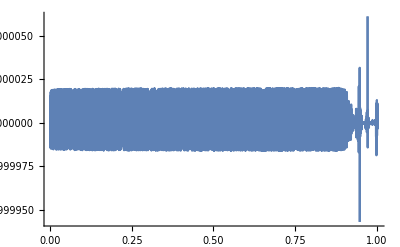

```mathematica
Plot[(ρ''[r]/d2ρdr2[ρ,r])/.sol,{r,Rmin,1+ρ1/2},PlotPoints->80]
```

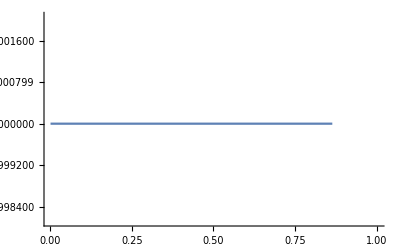

```mathematica
Plot[ApproxDensity''[r]/d2ρdr2[ApproxDensity,r],{r,Rmin,1+ρ1/2},PlotPoints->80]
```

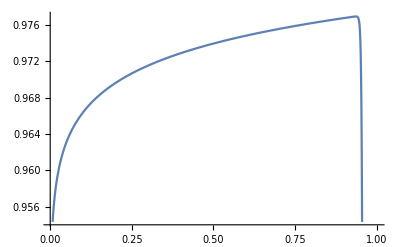

```mathematica
Plot[ApproxDensity[r]/(ρ[r]/.sol),{r,Rmin,1+ρ1/2},PlotPoints->80]
```